```mathematica
(*1*)
```

```mathematica
DSolve[{y'[x]==1/((1/2)*((y[x]*x)+(3*((y[x])^2)*(Exp[x^2]))))},y[x],x];
DSolve[{y'[x]==1/((1/2)*((y[x]*x)+(3*((y[x])^2)*(Exp[x^2])))),y[((1/2)+5)]==(1/2)},y[x],x]
```

DSolve[{y'[x]==2/(x y[x]+3 ⅇ^(x^2) y[x]^2),y[11/2]==1/2},y[x],x]

```mathematica
(*Como se puede ver, no tiene solución en el punto y(11/2) = 1/2 ya que no es continua allí o no está definida.*)
```

```mathematica
(*II*)
DSolve[{y'[x]==(((y[x])+(Sqrt[x*y[x]]))/(x-y[x]-((y[x]^(-1/2))*(x^(3/2)))))/y[x]},y[x],x] ;
```

DSolve[{y'[x]==(y[x]+√(x y[x]))/((x-x^(3/2)/(√y[x])-y[x]) y[x])},y[x],x]

```mathematica
DSolve[{y'[x]==(x-1)/y[x],y[-2]==1},y[x],x]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{{y[x]→√(-7-2 x+x^2)}}

```mathematica
(*3*)
Integrate[Sqrt[1/x],x]
```

2/(√(1/x))

```mathematica
Integrate[((1/2)*((x)/((x^2)+(1)))),x]
```

1/4 Log[1+x^2]

```mathematica
Derivative[Integrate[Sqrt[1/x],x]+Integrate[((1/2)*((x)/((x^2)+(1)))),x],x]
```

Derivative[2/(√(1/x))+1/4 Log[1+x^2],x]

```mathematica
(*La primera la multiplicamos por Sqrt[P(t)], luego, se obtiene la integral respecto de q para hallar g(p) y reemplazar...*)
```

```mathematica
(*III*)
```

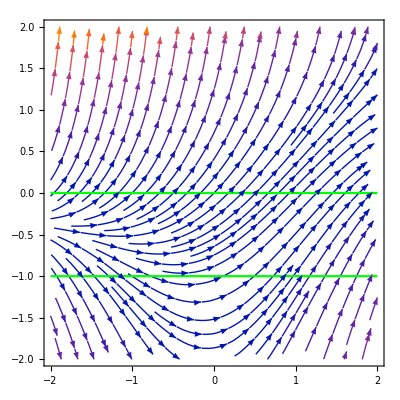

```mathematica
Show[StreamPlot[{1,Exp[y]-(x*y)},{x,-2,2},{y,-2,2}],ContourPlot[{y==-1,y==0},{x,-v2,2},{y,-2,2},ContourStyle->Green]]
```

```mathematica
Solve[Exp[y+c]-(x*y)==0,c]
```

{{c→ConditionalExpression[-y+2 ⅈ π C[1]+Log[x y], C[1]∈ℤ]}}

```mathematica
Derivative[Exp[y]-(x*y)==0,x]
```

Derivative[ⅇ^y-x y==0,x]